# Задача 4. ОДУ

## Търсим точно решение

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x]-Log[x^2+1]+(2x)/(x^2+1)+4,y[x],x]
```

{{y[x]→-4+ⅇ^x C[1]+Log[1+x^2]}}

## Търсим частно решение

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x]-Log[x^2+1]+(2x)/(x^2+1)+4, y[6]==10},y[x],x]
```

{{y[x]→(-4 ⅇ^6+14 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6}}

## Визуализация на точното решение

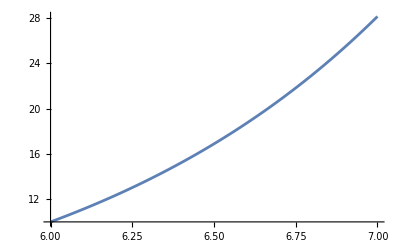

```mathematica
yt[x_]:=(-4 ⅇ^6+14 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
tochno = Plot[yt[x], {x, 6, 7}]
```

Извод : Не можем да намерим точно решение с аналитичен метод

## Търсим Приближено (числено) решение

#### h = 0.2

## Метод на Рунге - Кута с четири междинни точки

```mathematica
(*въвеждаме условието на задачата*)
a = 6; b = 7;
x = a;
y = 10.;
points = {{x,y}};
f[x_,y_]:=  y-Log[x^2+1]+(2x)/(x^2+1)+4
(*съставяме мрежата*)
h = 0.2;
n = (b-a)/h;
```

i = 0 x_i = 6 y_i = 10. f(x_i, y_i) = 10.7134 y_точно(x_i) = 10 грешка = 0.

i = 1 x_i = 6.2 y_i = 12.364 f(x_i, y_i) = 13.0036 y_точно(x_i) = 12.364 грешка = 0.000028465

i = 2 x_i = 6.4 y_i = 15.2353 f(x_i, y_i) = 15.8037 y_точно(x_i) = 15.2354 грешка = 0.000069588

i = 3 x_i = 6.6 y_i = 18.7269 f(x_i, y_i) = 19.2262 y_точно(x_i) = 18.727 грешка = 0.000127575

i = 4 x_i = 6.8 y_i = 22.9764 f(x_i, y_i) = 23.409 y_точно(x_i) = 22.9766 грешка = 0.000207875

i = 5 x_i = 7. y_i = 28.1522 f(x_i, y_i) = 28.5201 y_точно(x_i) = 28.1525 грешка = 0.000317522

Теоретичната локална грешка е 0.00032

Теоретичната глобална грешка е 0.0016

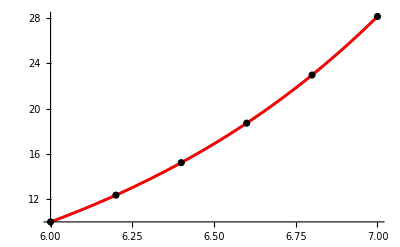

```mathematica
For[i =0, i≤n, i++,
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f(x_i, y_i) = ", f[x,y], " y_(:0442:043e:0447:043d:043e)(x_i) = ", yt[x], " грешка = ", Abs[y-yt[x]]];
k1 =h*f[x,y];
k2 =h*f[x+1/2 h,y+1/2 k1];
k3 =h*f[x+1/2 h,y+1/2 k2];
k4 =h*f[x+h,y+k3];
y = y + 1/6(k1+2k2+2k3+k4);
x = x+h;
AppendTo[points,{x,y}]
]
Print["Теоретичната локална грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
grp = ListPlot[points, PlotStyle->{Black}];
grf = Plot[yt[x],{x,a,b}, PlotStyle->Red];
Show[tochno, grf, grp]
```

## Модифициран метод на Ойлер

```mathematica
(*въвеждаме условието на задачата*)
a = 6; b = 7;
x = a;
y = 10.;
points = {{x,y}};
f[x_,y_]:=  y-Log[x^2+1]+(2x)/(x^2+1)+4
(*съставяме мрежата*)
h = 0.2;
n = (b-a)/h;
```

Мрежата е с n = 5. и стъпка h = 0.2

Теоретичната локална  грешка е 0.008

Теоретичната глобална грешка е 0.04

i = 0 x_i = 6 y_i = 10. f_i = 10.7134 x_(i + 1/2) = 6.1 y_(i + 1/2) = 11.0713 f_(i + 1/2) = 11.7475 y_точно = 10 истинска грешка = 0.

i = 1 x_i = 6.2 y_i = 12.3495 f_i = 12.9891 x_(i + 1/2) = 6.3 y_(i + 1/2) = 13.6484 f_(i + 1/2) = 14.2521 y_точно = 12.364 истинска грешка = 0.0145277

i = 2 x_i = 6.4 y_i = 15.1999 f_i = 15.7683 x_(i + 1/2) = 6.5 y_(i + 1/2) = 16.7768 f_(i + 1/2) = 17.3103 y_точно = 15.2354 истинска грешка = 0.0354807

i = 3 x_i = 6.6 y_i = 18.662 f_i = 19.1614 x_(i + 1/2) = 6.7 y_(i + 1/2) = 20.5781 f_(i + 1/2) = 21.0439 y_точно = 18.727 истинска грешка = 0.0649866

i = 4 x_i = 6.8 y_i = 22.8708 f_i = 23.3034 x_(i + 1/2) = 6.9 y_(i + 1/2) = 25.2011 f_(i + 1/2) = 25.6012 y_точно = 22.9766 истинска грешка = 0.105799

i = 5 x_i = 7. y_i = 27.991 f_i = 28.359 x_(i + 1/2) = 7.1 y_(i + 1/2) = 30.8269 f_(i + 1/2) = 31.1633 y_точно = 28.1525 истинска грешка = 0.161472

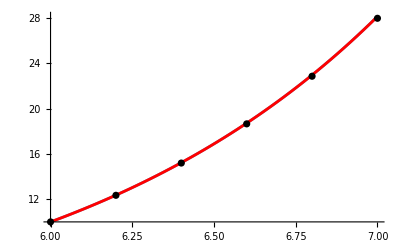

```mathematica
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
x12 = x+h/2;
y12 = y +h/2*f[x,y];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " x_(i + 1/2) = ",x12, " y_(i + 1/2) = ",y12, " f_(i + 1/2) = ",f[x12,y12], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x12,y12];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[tochno, gryt,grp]
```